```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];
<<gPlots.m;
Needs["gPlots`"];

G[v_,{p_,λ_,μ_}]:=μ*Exp[λ*(Dot[Normalize[v],Normalize[p]]-1)];
(*All-Frequency Eq(3)*)
G1[θ_,λ_]:=Exp[λ*(Cos[θ]-1)];

Print[">Solve θ:"]
Solve[G1[θ,λ]==ϵ&&ϵ>0&&λ>-Log[ϵ],θ,Reals]
```

>Solve θ:

{{θ→ConditionalExpression[-ArcCos[(λ+Log[ϵ])/λ]+2 π C[1],(C[1]∈ℤ&&0<ϵ<1&&λ+Log[ϵ]>0)||(C[1]∈ℤ&&ϵ>1&&λ+Log[ϵ]>0&&2 λ+Log[ϵ]≤0)]},{θ→ConditionalExpression[ArcCos[(λ+Log[ϵ])/λ]+2 π C[1],(C[1]∈ℤ&&0<ϵ<1&&λ+Log[ϵ]>0)||(C[1]∈ℤ&&ϵ>1&&λ+Log[ϵ]>0&&2 λ+Log[ϵ]≤0)]}}

>Solve θ:

>Solve θ:

{{θ→ConditionalExpression[-ArcCos[(λ+Log[ϵ])/λ]+2 π C[1],(C[1]∈ℤ&&0<ϵ<1&&λ+Log[ϵ]>0)||(C[1]∈ℤ&&ϵ>1&&λ+Log[ϵ]>0&&2 λ+Log[ϵ]≤0)]},{θ→ConditionalExpression[ArcCos[(λ+Log[ϵ])/λ]+2 π C[1],(C[1]∈ℤ&&0<ϵ<1&&λ+Log[ϵ]>0)||(C[1]∈ℤ&&ϵ>1&&λ+Log[ϵ]>0&&2 λ+Log[ϵ]≤0)]}}

```mathematica
Print[">Failed to solve integral"];
SolveFa[λ_,ϵ_]=Integrate[G1[θ,λ],{θ,0,ArcCos[1+Log[ϵ]/λ]}]
```

>Failed to solve integral

∫_0^ArcCos[1+Log[ϵ]/λ] ⅇ^(λ (-1+Cos[θ]))ⅆθ

>Inverse Function: (0.1 ⅇ^(0.159155 #1)&)

{>Validate Inverse Function: (1./(1/x)^1.==x)}

>Area Integral: λ_max=30, Area_max=35

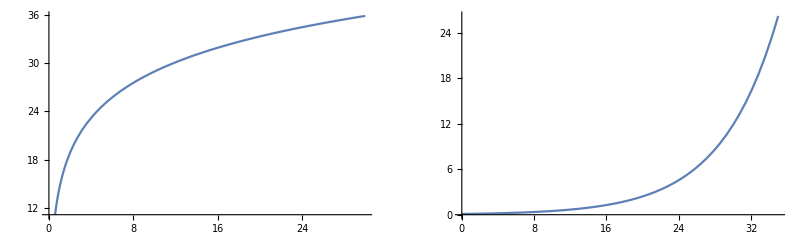

```mathematica
Subscript[f, a][λ_,ϵ_]=-2π*Log[ϵ/λ];//N
DefaultEpsilon=0.1;

Fa[λ_]:=Subscript[f, a][λ,DefaultEpsilon];
InvFa=InverseFunction[Fa];
Print[">Inverse Function:" TraditionalForm[InvFa]];
Print[">Validate Inverse Function:" {InvFa[Fa[x]]==x}]

Print[">Area Integral: λ_max=30, Area_max=35"];
{Plot[Fa[λ],{λ,0.01,30}],Plot[InvFa[area],{area,0,35}]}//GraphicsRow
```

```mathematica
(*https://neil3d.github.io/assets/pdf/s2013_pbs_epic_notes_v2.pdf Page 12*)
FallOff[r_,d_]:=(Clip[(1-(d/r)^4),{0,1}])^2/(d^2+1);

DefaultLightingPower=1;
pi=N[π];
DefaultLightCenter={-1,1};
LightCircle[c_,r_,θ_]:=c+r*{Cos[θ],Sin[θ]};
FallOffPaint[θ_,lightRadius_]:=Module[{x,normal,d,nol},
x={θ-π,0};
normal={0,1};
d=Norm[DefaultLightCenter-x];
nol=Dot[normal,Normalize[DefaultLightCenter-x]];
{x[[1]],FallOff[lightRadius,d]*DefaultLightingPower}
];

Print[">Falloff(Ground Lighting):"]
Manipulate[ParametricPlot[{
LightCircle[DefaultLightCenter,r,θ],
FallOffPaint[θ,r]
},
{θ,0,2π}, 
PlotRange->{{-3,3},{-3,3}},AspectRatio->1],{r,2,5}]
```

>Falloff(Ground Lighting):

```mathematica
NoLFallOffPaint[θ_,lightRadius_]:=Module[{x,normal,d,nol},
x={θ-π,0};
normal={0,1};
d=Norm[DefaultLightCenter-x];
nol=Clip[Dot[normal,Normalize[DefaultLightCenter-x]],{0,1}];
{x[[1]],nol*FallOff[lightRadius,d]*DefaultLightingPower}
];

Print[">NoL*FallOff(Ground Lighting):"]
Manipulate[ParametricPlot[{LightCircle[DefaultLightCenter,r,θ],NoLFallOffPaint[θ,r]},
{θ,0,2π}, PlotRange->{{-3,3},{-3,3}},AspectRatio->1],{r,2,5}]
```

>NoL*FallOff(Ground Lighting):

```mathematica
(*   
    i: SG vector in light domain
  x: shading point
  l: light point
r: light radius
s: light intensity
*)
ApproxLight[i_,x_,l_,r_,s_]:=Module[
{d,p,λ,μ},
d=Norm[l-x];
p=(l-x)/d;
λ=InvFa[2π*r^2/d^2];
μ=s/d^2;
G[i,{p,λ,μ}]
];

(*θ must between -π/2 and π/2*)
GSimple[θ_,λ_,μ_]:=If[-π/2≤θ≤π/2,μ*Exp[λ*(Cos[θ]-1)],0];
ApproxLight2[θ_,x_,l_,r_,s_]:=Module[
{d,p,λ,μ},
d=Norm[l-x];
p=(l-x)/d;
λ=InvFa[2π*r^2/d^2];
μ=s/d^2;
GSimple[θ,λ,μ]
];

ApproxLightPaint[θ_,shadingPos_,lightPos_,lightRadius_,lightIntensity_]:=Module[
{SGShading},
SGShading=ApproxLight2[θ,shadingPos,lightPos,lightRadius,lightIntensity];
shadingPos+{θ,SGShading}
];
Print[">SG Light simulation at shading point(light-oriented SG):"]
Manipulate[ParametricPlot[{
LightCircle[DefaultLightCenter,radius,θ],
ApproxLightPaint[θ,{shadingPtX,0},DefaultLightCenter,radius,intensity],
LightCircle[{shadingPtX,0},0.1,θ]},
{θ,-π,π}, PlotRange->{{-3.5,3.5},{-3.5,3.5}},AspectRatio->1],
{radius,2,5},
{shadingPtX,-π,π},
{intensity,1,10}]
```

>SG Light simulation at shading point(light-oriented SG):

```mathematica
GSimple3[θ_,λ_,μ_]:=If[-π/2≤θ≤π/2,μ*Exp[λ*(Cos[θ]-1)],0];
ClipAngle[x_]:=Which[x>π,x-2π,x<-π,x+2π,True,x];
ApproxLight3[varAngleInLightDomain_,shadingPos_,lightPos_,lightRadius_,lightIntensity_]:=Module[
{d,axisAngle,angleOffset,p,λ,μ},
d=Norm[lightPos-shadingPos];
p=(lightPos-shadingPos)/d;
λ=InvFa[2π*lightRadius^2/d^2];
μ=lightIntensity/d^2;
axisAngle=ToPolarCoordinates[p][[2]];
angleOffset=ClipAngle[varAngleInLightDomain-axisAngle];
GSimple3[angleOffset,λ,μ]
];
ApproxLightPaint3[varAngleInLightDomain_,shadingPos_,lightPos_,lightRadius_,lightIntensity_]:=Module[
{sgShading,sgAxis,axisAngle,angleOffset,rt},
sgAxis=Normalize[lightPos-shadingPos];
axisAngle=ToPolarCoordinates[sgAxis][[2]];
angleOffset=ClipAngle[varAngleInLightDomain-axisAngle];
sgShading=ApproxLight3[varAngleInLightDomain,shadingPos,lightPos,lightRadius,lightIntensity];
	(RotationTransform[axisAngle+π/2,lightPos]/@{(lightPos+{angleOffset,sgShading})})[[1]]//N
];

LinePaint[θ_,originPos_,direction_]:=originPos+θ*Normalize[direction];

Print[">SG Light simulation at shading point(light-oriented SG):"]
Manipulate[ParametricPlot[{
LightCircle[DefaultLightCenter,radius,θ],
LightCircle[{shadingPtX,0},0.1,θ],
ApproxLightPaint3[θ,{shadingPtX,0},DefaultLightCenter,radius,intensity],
LinePaint[(θ+π)/2,DefaultLightCenter,({shadingPtX,0}-DefaultLightCenter)]},
{θ,-π,π}, 
PlotStyle->{Green,Green,Blue,Blue},
PlotRange->{{-3.5,3.5},{-3.5,3.5}},AspectRatio->1],
{radius,2,5},
{shadingPtX,-π,π},
{intensity,1,10}]
```

>SG Light simulation at shading point(light-oriented SG):

```mathematica
sgIntegral[λ_,μ_:1]:=μ*2π*(1-Exp[-2λ])/λ;
ApproxLight4[xOffset_,lightPos_,lightRadius_,lightIntensity_]:=Module[
{d,shadingPos,p1,λ1,μ1},
shadingPos={xOffset,0};
d=Norm[lightPos-shadingPos];
(*Point Light SG*)
p1=Normalize[lightPos-shadingPos];
λ1=InvFa[2π*lightRadius^2/d^2];
μ1=lightIntensity/d^2;

sgIntegral[λ1,μ1]
];
ApproxLightPaint4[xOffset_,lightPos_,lightRadius_,lightIntensity_]:=Module[
{sgEnergy1},
sgEnergy1=ApproxLight4[xOffset,lightPos,lightRadius,lightIntensity];
	{xOffset,sgEnergy1}
];

Print[">SG Light Energy(at Ground):"]
Manipulate[ParametricPlot[{
LightCircle[DefaultLightCenter,radius,xOffset],
ApproxLightPaint4[xOffset,DefaultLightCenter,radius,intensity]},
{xOffset,-π,π}, 
PlotStyle->{Green,Blue},
PlotRange->{{-3.5,3.5},{-3.5,3.5}},AspectRatio->1],
{radius,2,5},
{intensity,1,10}]
```

>SG Light Energy(at Ground):

```mathematica
DefaultDiffuseColor=1;
sgDot[{p1_,λ1_,μ1_},{p2_,λ2_,μ2_}]:=4π*μ1*μ2*Sinh[Norm[p1*λ1+p2*λ2]]/(Exp[λ1+λ2]*Norm[p1*λ1+p2*λ2]);
sgDiffuse[diffuseCol_,{p1_,λ1_,μ1_},{p2_,λ2_,μ2_}]=diffuseCol/π sgDot[{p1,λ1,μ1},{p2,λ2,μ2}];

DiffuseLighting=1;

ApproxLight5[xOffset_,lightPos_,lightRadius_,lightIntensity_]:=Module[
{d,shadingPos,p1,λ1,μ1,p2,λ2,μ2,diffuse},
shadingPos={xOffset,0};
d=Norm[lightPos-shadingPos];
(*Point Light SG*)
p1=Normalize[lightPos-shadingPos];
λ1=InvFa[2π*lightRadius^2/d^2];
μ1=lightIntensity/d^2;
(*Clamped Cosine SG*)
p2=p1;
λ2=2.01906;
μ2=1.077094;

sgDiffuse[DefaultDiffuseColor,{p1,λ1,μ1},{p2,λ2,μ2}]
];

ApproxLightPaint5[xOffset_,lightPos_,lightRadius_,lightIntensity_]:=Module[
{sgShading},
sgShading=ApproxLight5[xOffset,lightPos,lightRadius,lightIntensity];
	{xOffset,sgShading}
];

Print[">SG Diffse Lighting(at Ground):" HoldForm[Subscript[C, diffuse]/π*Convolve[Subscript[SG, light],Subscript[SG, ClampedCosine],p1,p2]]];
Manipulate[ParametricPlot[{
LightCircle[DefaultLightCenter,radius,xOffset],
ApproxLightPaint5[xOffset,DefaultLightCenter,radius,intensity]},
{xOffset,-π,π}, 
PlotStyle->{Green,Blue},
PlotRange->{{-3.5,3.5},{-3.5,3.5}},AspectRatio->1],
{radius,1,5},
{intensity,1,10}]
```

>SG Diffse Lighting(at Ground): (C_diffuse Convolve[SG_light,SG_ClampedCosine,p1,p2])/π

```mathematica
Print[">New Fit SG Diffse Lighting(at Ground):" HoldForm[Subscript[C, diffuse]/π]*HoldForm[Subscript[SG, light]⊗Subscript[SG, ClampedCosine]]];

sgAmplitude6[t_,a_,b_,c_]=a*t^2+b*t+c;
sgSharpness6[percent_,d_,e_,f_]=d*percent^2+e*percent+f;

RadiusParams={
{0.791375,-1.89057,1.0872,6.66654,-10.8249,6.76642},
{-0.340146,0.0665636,0.236471,3.79125,0.618155,1.38885},
{0.385139,-0.87285,0.485253,1.80957,0.308354,2.7173},
{0.213239,-0.506706,0.291679,1.83615,2.49729,1.51728},
{0.128335,-0.316743,0.187358,2.15074,3.59944,0.786432}};

ApproxLight6[xOffset_,lightPos_,lightRadius_,lightIntensity_]:=Module[
{d,distPercent,shadingPos,p1,λ1,μ1,p2,λ2,μ2,diffuse},
shadingPos={xOffset,0};
d=Norm[lightPos-shadingPos];
distPercent=d/lightRadius;
(*Point Light SG*)
p1=Normalize[lightPos-shadingPos];
λ1=sgSharpness6[distPercent,
RadiusParams[[lightRadius]][[4]],RadiusParams[[lightRadius]][[5]],RadiusParams[[lightRadius]][[6]]];
μ1=lightIntensity*sgAmplitude6[distPercent,
RadiusParams[[lightRadius]][[1]],RadiusParams[[lightRadius]][[2]],RadiusParams[[lightRadius]][[3]]];
(*Clamped Cosine SG*)
p2=p1;
λ2=2.01906;
μ2=1.077094;

sgDiffuse[DefaultDiffuseColor,{p1,λ1,μ1},{p2,λ2,μ2}]
];

ApproxLightPaint6[xOffset_,lightPos_,lightRadius_,lightIntensity_]:=Module[
{sgShading},
sgShading=ApproxLight6[xOffset,lightPos,lightRadius,lightIntensity];
	{xOffset,sgShading}
];

Manipulate[ParametricPlot[{
LightCircle[DefaultLightCenter,radius,xOffset],
ApproxLightPaint6[xOffset,DefaultLightCenter,radius,intensity]},
{xOffset,-π,π}, 
PlotStyle->{Green,Blue},
PlotRange->{{-3.5,3.5},{-3.5,3.5}},AspectRatio->1],
{radius,1,5,1},
{intensity,1,10}]
```

>New Fit SG Diffse Lighting(at Ground): C_diffuse/π SG_light⊗SG_ClampedCosine